```mathematica
Table[GraphicsRow[Catenate[Table[
SeedRandom[111180+i];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,j],{2}],0},{85,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)], {j,1, 5}]&/@ {<||>, 1}]], {i, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[Catenate[Table[
SeedRandom[111180+7];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,j],{2}],0},{85,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]], {j,1, 5}]&/@ {<||>, 1}]]
```

-Graphics-

```mathematica
SeedRandom[111180+7];ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{85,{-5, 15}}, 1][[2]]
```

```mathematica
ResourceFunction["PerturbedCellularAutomaton"]
```

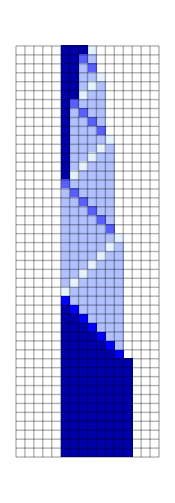
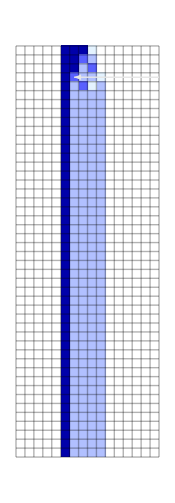

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
{ca, capert} = First[[rule, {Join[Table[1,3],{2}],0},{45,{-5, 10}}, #]]&/@ {<||>, pert};
Row[MapThread[{{"[◼]", "PerturbedArrayPlot"}}[#1, #2,ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.3], "ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, "InitialIndex"->0, ImageSize->175] &,{{ca, capert},  {{}, First[Keys[pert]]}}
], Spacer[200]]]
```

```mathematica
MapAt[ArrayPlot, caperts, {All,All, 1}]
```

```mathematica
{{{-Graphics-,<||>},{-Graphics-,<||>}},{{-Graphics-,<|{3,7}->4|>},{-Graphics-,<|{3,7}->4|>}}}[[1]]
```

{{-Graphics-,<||>},{-Graphics-,<||>}}

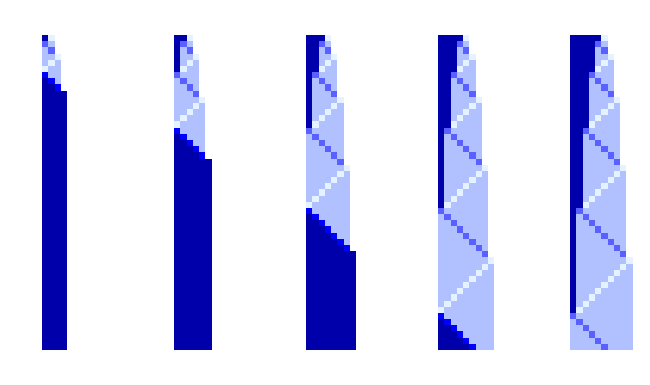
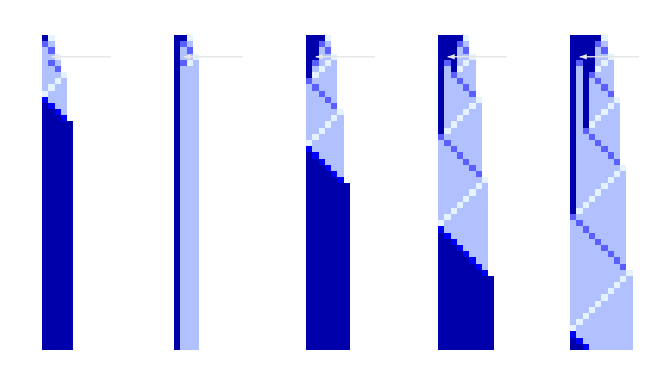
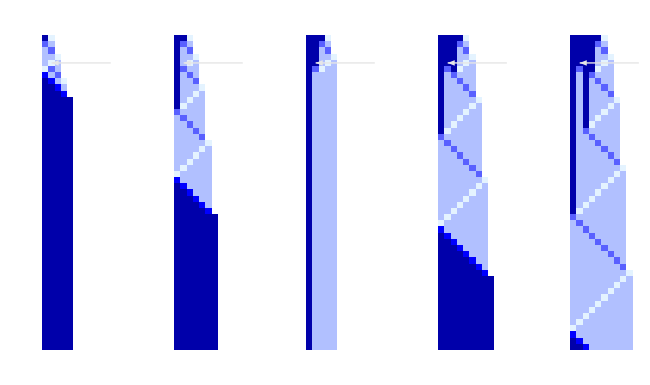
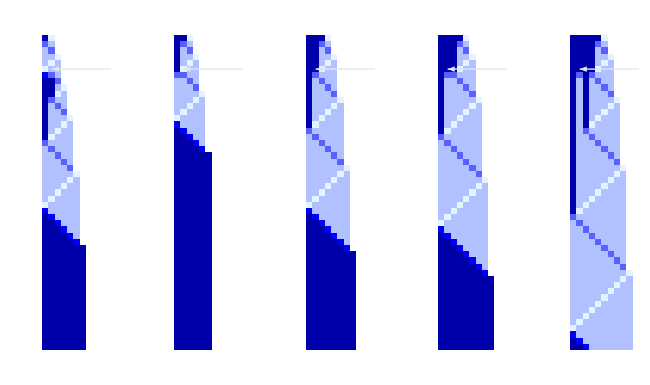
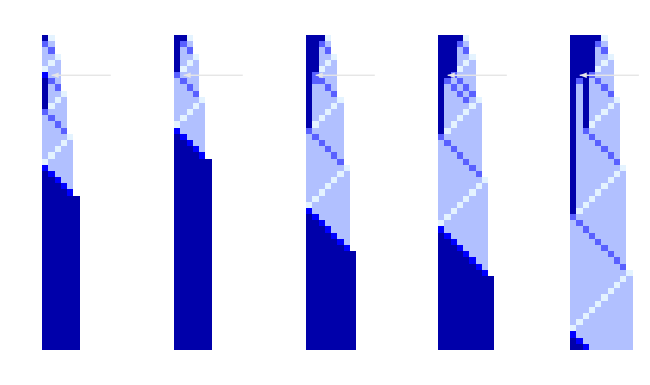
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{k,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{50,{-5, 10}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->False, "ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left]]@@@#]&/@caperts
], {k, 4, 7}]
```

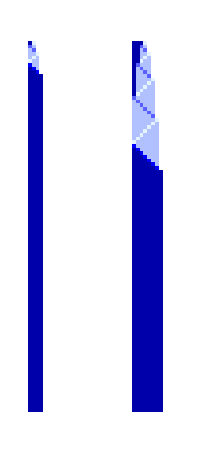
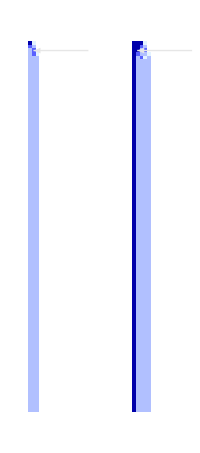

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{100,{-5, 15}}, #], {j, {1, 3}}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->False, "ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left]]@@@#]&/@caperts
]
```

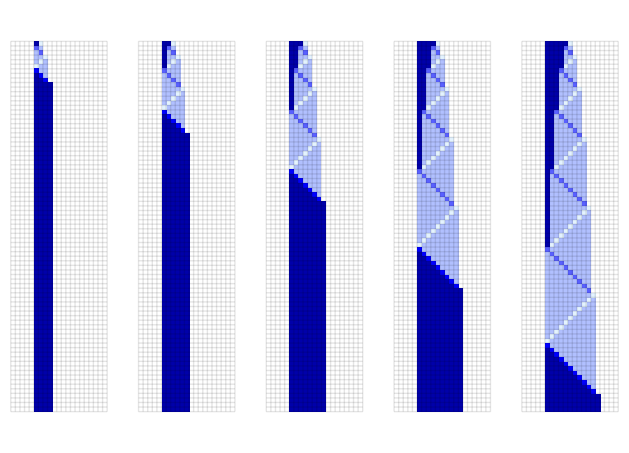
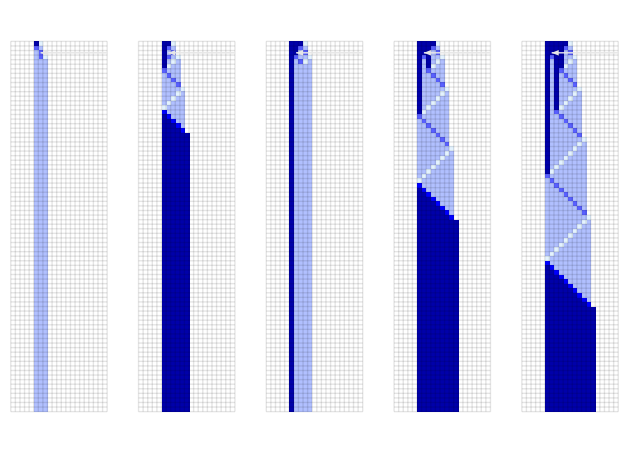

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left]]@@@#]&/@caperts
]
```

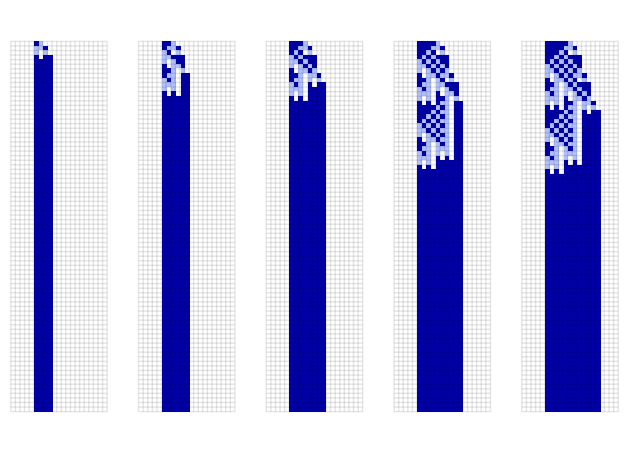
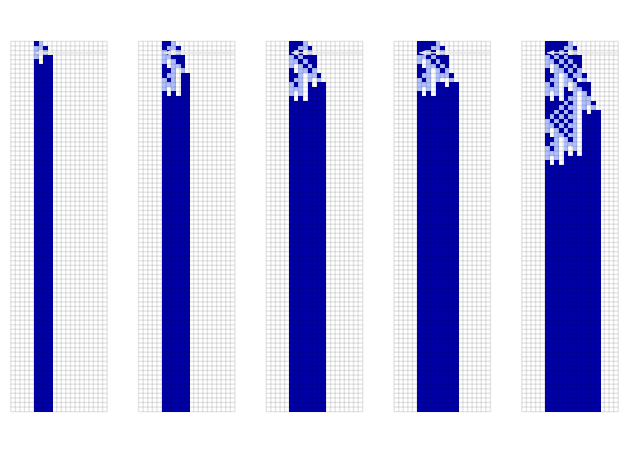

```mathematica
Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{3,6}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left]]@@@#]&/@caperts
]
```

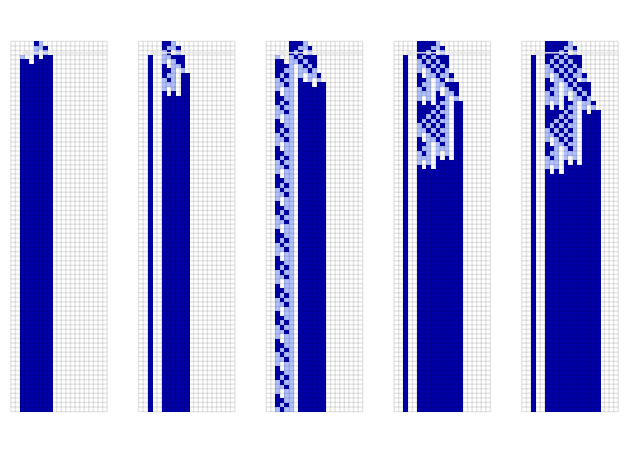
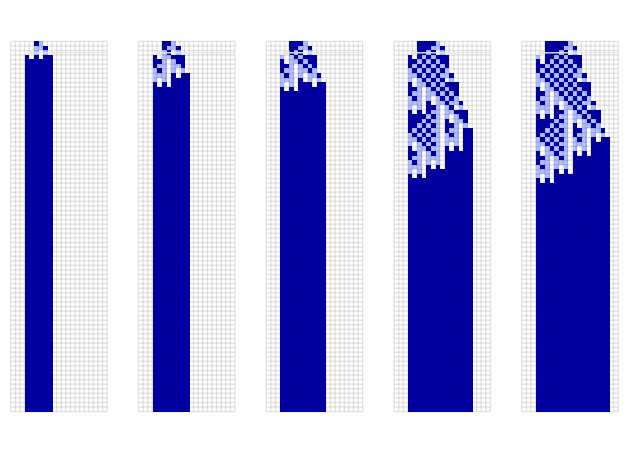
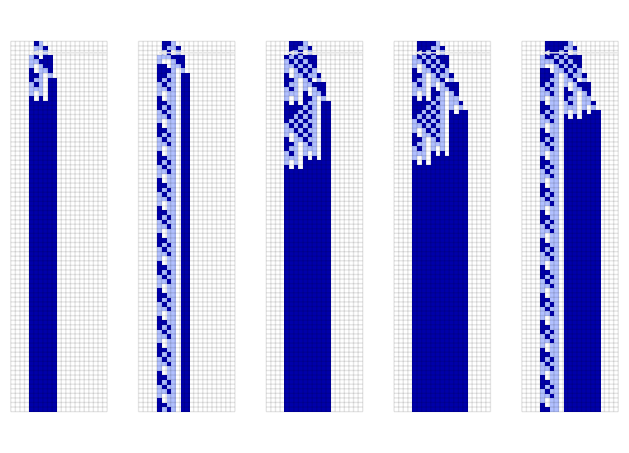
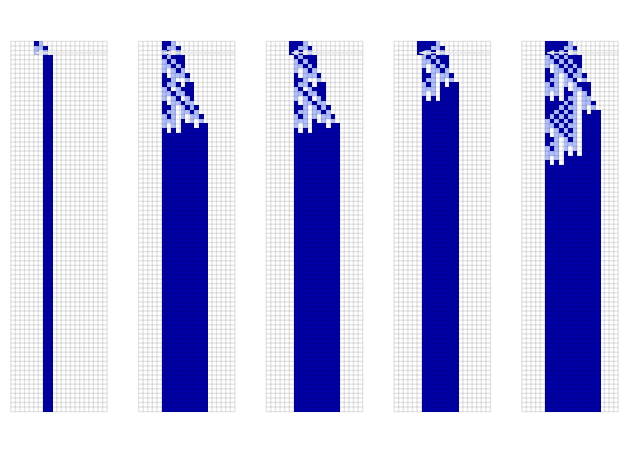
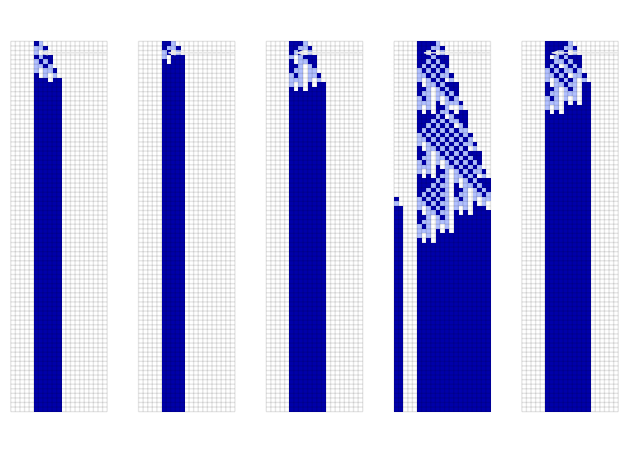
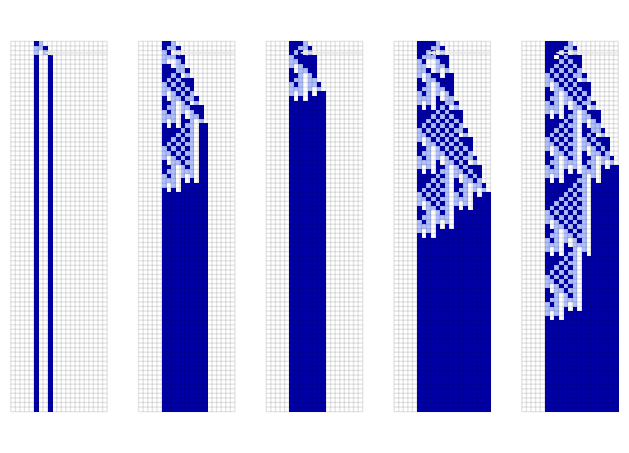
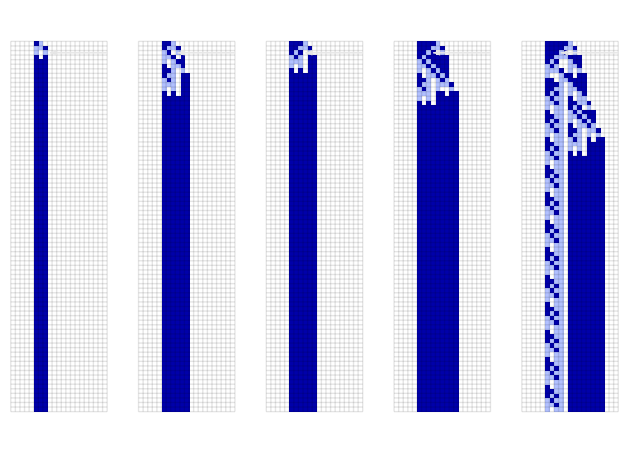
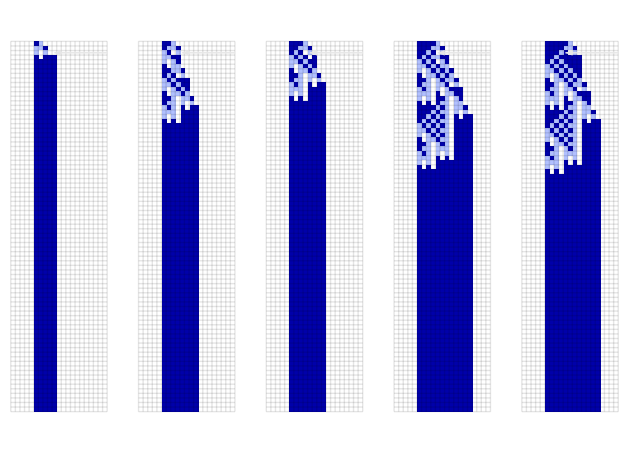
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[
SeedRandom[111000+k];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{3,k}->"Random"|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left]]@@@#]&/@caperts
], {k, 3, 10}]
```

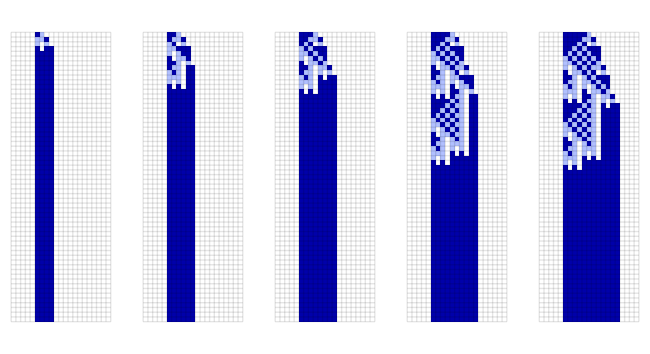
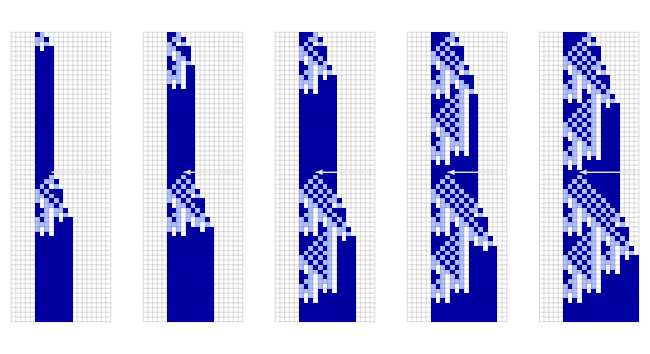

```mathematica
SeedRandom[111000+8];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{30,9}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{60,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left]]@@@#]&/@caperts
]
```

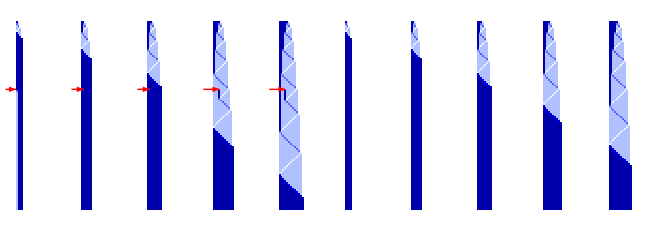
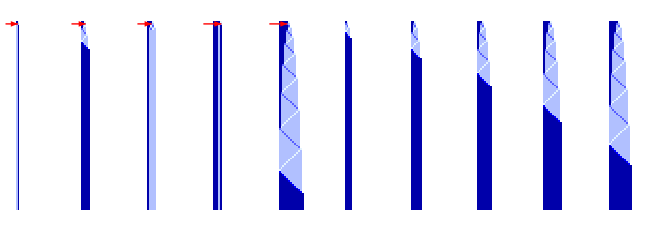
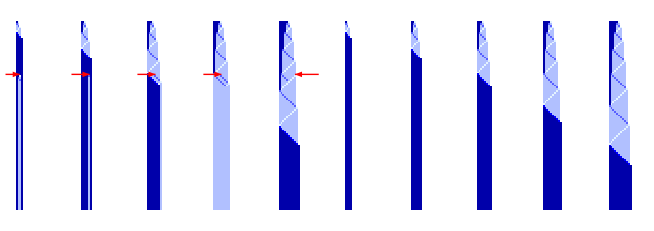
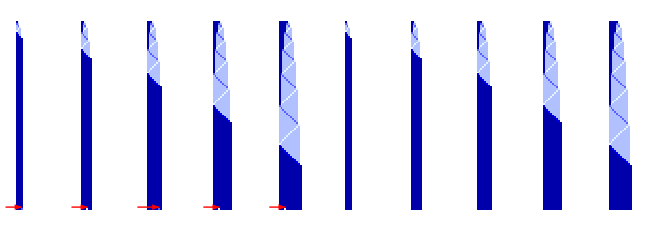
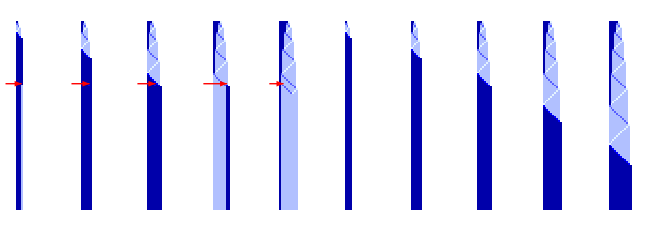

```mathematica
Table[Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
GraphicsRow[Catenate[Table[SeedRandom[100000 + k];{{"[◼]", "PerturbedArrayPlot"}}[#1, If[#2=== <||>, {}, First[Keys[#2]]], ColorRules->colrules, Mesh->False]&@@[rule, {Join[Table[1,j],{2}],0},{100,{-5, 20}}, Sequence@@#], {j, 1, 5}]&/@ {{{RandomChoice, RandomChoice}->"Random", "Body"->True}, {<||>}}
]]], {k, 1, 5}]
```

```mathematica
[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, {Join[Table[1,3],{2}],0},{50,{-5, 10}}, {8, -3}, "Body"->True][[2]]
```

<|{8,8}→0|>

#### Final

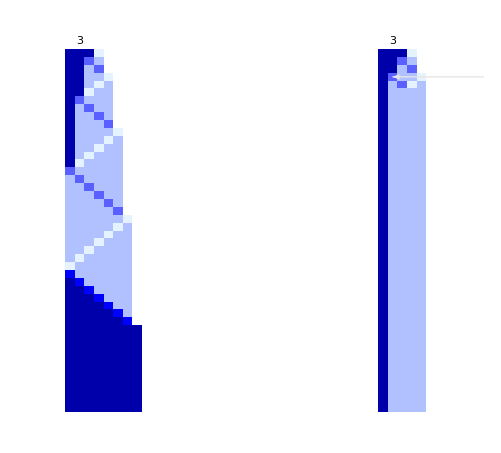

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
{ca, capert} = First[[rule, {Join[Table[1,3],{2}],0},{45,{-5, 10}}, #]]&/@ {<||>, pert};
GraphicsRow[MapThread[Show[{{"[◼]", "PerturbedArrayPlot"}}[#1, #2,ColorRules->colrules, Mesh->False, MeshStyle->Opacity[.3], "ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, "InitialIndex"->0, ImageSize->175,(*FrameStyle-> If[#2 =!={},Directive[Thickness[.01], Red], Automatic], *)
(*FrameStyle->Directive[Thickness[.01], GrayLevel[.3]],*)
Frame->None,
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],FrameTicks->{False,  False, False,({{1 + #,"", {-.01, .05}}, {4 + #, "", {-.01, .05}}}&[4.5])}], Graphics[Text["3", {6.5, Length[ca] + 1}]]] &,{{ca, capert},  {{}, First[Keys[pert]]}}
], Spacings->100]]
```

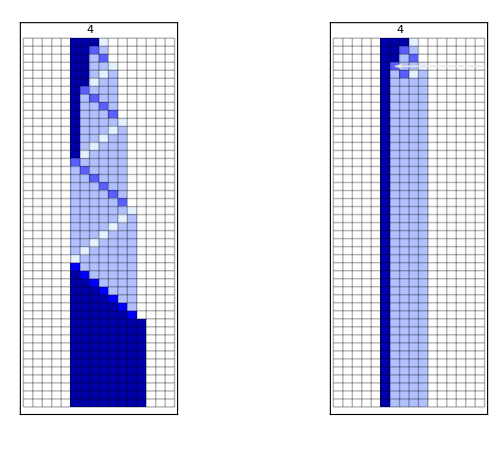

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
{ca, capert} = First[[rule, {Join[Table[1,3],{2}],0},{45,{-5, 10}}, #]]&/@ {<||>, pert};
GraphicsRow[MapThread[Show[{{"[◼]", "PerturbedArrayPlot"}}[#1, #2,ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.3], "ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, "InitialIndex"->0, ImageSize->175,
Frame->False,
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],FrameTicks->{False,  False, False,({{1 + #,"", {-.01, .05}}, {5 + #, "", {-.01, .05}}}&[4.5])}], Graphics[Text["4", {7, Length[ca] + 1}]], Frame->True, PlotRangePadding->{{Automatic, Automatic}, {Automatic, -.75}}] &,{{ca, capert},  {{}, First[Keys[pert]]}}
], Spacings->100]]
```

```mathematica
GraphicsRow[
MapIndexed[Function[{val, idx},SeedRandom[111010+ idx[[1]]];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,3],{2}],0},{40,{-5,12}}, val], Mesh->True, "Trim"->{None, None}, ColorRules->None, ColorFunction->(Blend[{White, Blue}, #]&)]], Prepend[Table[1, 4], <||>]]]
```

-Graphics-

```mathematica
GraphicsRow[
MapIndexed[Function[{val, idx},SeedRandom[111010+ idx[[1]]];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,3],{2}],0},{40,{-5,12}}, val], Mesh->True, "Trim"->{None, None}, ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}]], Prepend[Table[1, 4], <||>]]]
```

-Graphics-

```mathematica
SeedRandom[111010+ 5];ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,3],{2}],0},{40,{-5,12}}, 1][[2]]
```

<|{27,11}→2|>

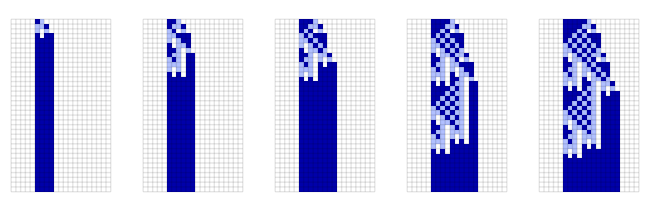

```mathematica
GraphicsRow[
Table[
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,j],{2}],0},{35,{-5,15}}, {}], Mesh->True, "Trim"->{None, None}, ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}], {j, 1, 5}]]
```

```mathematica
GraphicsRow[
Table[
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,j],{2}],0},{35,{-5,15}}, <|{6,8}->1|>], Mesh->True, "Trim"->{None, None}, ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}], {j, 1, 5}]]
```

-Graphics-

```mathematica
GraphicsRow[
Table[
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,j],{2}],0},{35,{-5,15}}, <|{3,8}->2|>], Mesh->True, "Trim"->{None, None}, ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}], {j, 1, 5}]]
```

-Graphics-

```mathematica
LightBlue
```

```mathematica
RGBColor[0.58, 0.8300000000000001, 1.]
```

```mathematica
Blend[{White, LightBlue, Blue}, #/5]&/@ Table[i, {i, 5}]
```

{RGBColor[0.948, 0.976, 1.],RGBColor[0.896, 0.952, 1.],RGBColor[0.696, 0.752, 1],RGBColor[0.348, 0.376, 1],RGBColor[0, 0, 1]}